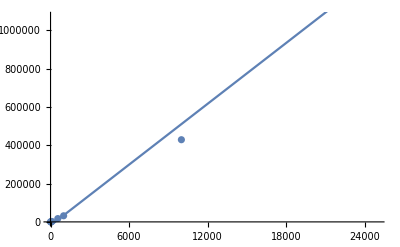

```mathematica
data={{5,29},{10,97},{55,1061},{100,2251},{555,17321},{1000,31933},{10000,428949},{100000,5278965}};
lp = ListPlot[data];
line = Fit[data,{1,x},x];
Show[lp,Plot[line,{x,0,25000}]]
```

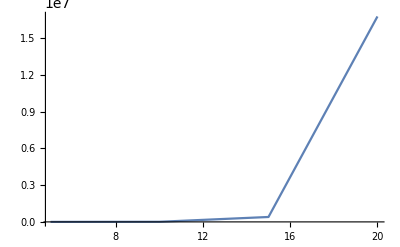

```mathematica
data2 = {{5,149},{10,8701},{15,401405},{20,16777213}};
lp2=ListPlot[data2,Joined->True];
line2=Fit[data2,{E^x},x];
Show[lp2,Plot[line2,{x,0,16777213}]]
```

```mathematica
FindFit[data2,a 2^x,{a},x]
```

{a→15.9963}

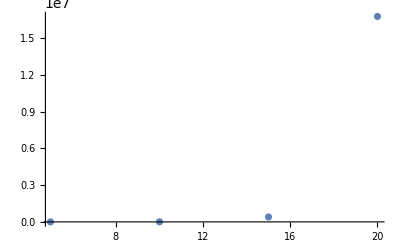

```mathematica
Show[ListPlot[data2],Plot[a 2^x/.{a->15.99633136043698},{x,5,100}]]
```